```mathematica
ArrayPlot[RandomInteger[1,{1050,1680}]]
```

-Graphics-

```mathematica
randisk[null_]:=Block[{ranint0=RandomInteger[{1,1050}]},DiskMatrix[RandomInteger[{1,IntegerPart[ranint0/2]}],ranint0]]
```

```mathematica
ArrayPlot[randisk[0]]
```

-Graphics-

```mathematica
ranpad[array_]:=Block[{ranint1=RandomInteger[1050-Length[Array]],ranint2=RandomInteger[1680-Length[Array]]},ArrayPad[array,{{ranint1,1050-(ranint1+Length[array])},{ranint2,1680-(ranint2+Length[array])}}]]
ArrayPlot[ranpad[DiskMatrix[100,200]]]
```

-Graphics-

```mathematica
twepm=ranpad[DiskMatrix[100,200]];
Length[twepm]
Length[Transpose[twepm]]
```

1050

1680

```mathematica
Monitor[Block[{i=0},For[sum=ranpad[randisk[0]],i<2,sum=Mod[sum+ranpad[DiskMatrix[100,200]],2]];sum],i]
```

$Aborted

```mathematica
Mod[({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}),2]
```

{{1,0,1},{0,1,0},{1,0,1}}

```mathematica
Timing[ArrayPlot[Block[{ranint0=RandomInteger[{1,1050}]},Block[{ranint1=RandomInteger[1050-ranint0],ranint2=RandomInteger[1680-ranint0]},ArrayPad[DiskMatrix[RandomInteger[{1,IntegerPart[ranint0/2]}],ranint0],{{ranint1,1050-(ranint1+ranint0)},{ranint2,1680-(ranint2+ranint0)}}]]]]]
```

{0.08503,-Graphics-}

```mathematica
randpiece[x_]:=Block[{ranint0=RandomInteger[{1,1050}]},Block[{ranint1=RandomInteger[1050-ranint0],ranint2=RandomInteger[1680-ranint0]},ArrayPad[DiskMatrix[RandomInteger[{1,IntegerPart[ranint0(*/2*)]}],ranint0],{{ranint1,1050-(ranint1+ranint0)},{ranint2,1680-(ranint2+ranint0)}}]]]
```

```mathematica
Mod[Sum[randpiece[0],{i,1,100}],2]//ArrayPlot
```

-Graphics-

```mathematica
addpiece[array_]:=Mod[array+randpiece[0],2]
addpiece30[array_]:=Transpose[Partition[one30[Flatten[Mod[array+randpiece[0],2]]],1050]]
addpiece184[array_]:=Transpose[Partition[one184[Flatten[Mod[array+randpiece[0],2]]],1050]]
```

```mathematica
Nest[addpiece,randpiece[0],200]//ArrayPlot
```

-Graphics-

```mathematica
one30[list_]:=Last[CellularAutomaton[30,list,2]]
one110[list_]:=Last[CellularAutomaton[110,list,2]]
one184[list_]:=Last[CellularAutomaton[184,list,2]]
```

```mathematica
ArrayPlot[addpiece30[randpiece[0]]]
```

-Graphics-

```mathematica
ArrayPlot[Nest[addpiece184,randpiece[0],150]]
```

-Graphics-

```mathematica
try=Nest[addpiece,randpiece[0],300];
try30=Nest[addpiece30,randpiece[0],300];
ArrayPlot[try]
ArrayPlot[Transpose[Partition[one30[one30[Flatten[try]]],1050]]]
ArrayPlot[Transpose[Partition[one110[one110[Flatten[try]]],1050]]]
ArrayPlot[try30]
ArrayPlot[Transpose[Partition[one30[one30[Flatten[try30]]],1050]]]
ArrayPlot[Transpose[Partition[one110[one110[Flatten[try30]]],1050]]]
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

```mathematica
{Mean[Flatten[try]]//N,Mean[Flatten[Transpose[Partition[one30[one30[Flatten[try]]],1050]]]]//N,Mean[Flatten[Transpose[Partition[one110[one110[Flatten[try]]],1050]]]]//N,Mean[Flatten[try30]]//N,Mean[Flatten[Transpose[Partition[one30[one30[Flatten[try30]]],1050]]]]//N,Mean[Flatten[Transpose[Partition[one110[one110[Flatten[try30]]],1050]]]]//N}
```

{0.486556,0.35705,0.29515,0.50093,0.500429,0.535088}

```mathematica
0.47728287981859413
0.36525340136054424
0.3013843537414966
0.5001763038548753
0.49956689342403626
0.5349126984126984

0.5025192743764172
0.369359410430839
0.3018015873015873
0.5011638321995465
0.5001581632653062
0.535625283446712
```

```mathematica
GameOfLife={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
onegol[array_]:=Last[CellularAutomaton[GameOfLife,array,2]]
```

```mathematica
CellularAutomaton[GameOfLife,try,5];
```

```mathematica
Map[ArrayPlot,%]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[try]
```

1050

```mathematica
ArrayPlot[Transpose[Partition[one30[one30[Flatten[try]]],1050]]]
```

-Graphics-

```mathematica
randswitch[x_]:=IntegerPart[Mod[2*Nest[Mod[1100087778366101933*#+12586269043,2305843009213693951]&,x,5]/2305843009213693951,2]]
```

```mathematica
ArrayPlot[Map[randswitch,try,{2}]]
```

$Aborted

```mathematica
BaseForm[1278564309327778315/2305843009213693951//N,2]
```

0.1000110111110011_2

```mathematica
1278564309327778315/2305843009213693951
```

```mathematica
PrimeQ[2305843009213693951]
```

True

```mathematica
PrimeQ[1283839219676404755]
```

False

```mathematica
NextPrime[Fibonacci[88]]/2305843009213693951//N
```

0.477087

```mathematica
NextPrime[Fibonacci[50]]
```

12586269043

```mathematica
ArrayPlot[ArrayFlatten[({{Nest[addpiece30,randpiece[0],100], Nest[addpiece30,randpiece[0],100]}, {Nest[addpiece30,randpiece[0],100], Nest[addpiece30,randpiece[0],100]}})]]
```

```mathematica
Monitor[Table[Export[StringJoin["fuzz",StringJoin[Map[ToString,ConstantArray[0,5-StringLength[ToString[m]]]]],ToString[m],".jpg"],ImageResize[ImageCrop[ArrayPlot[ArrayFlatten[({{Nest[addpiece30,randpiece[0],150], Nest[addpiece30,randpiece[0],150]}, {Nest[addpiece30,randpiece[0],150], Nest[addpiece30,randpiece[0],150]}})],Frame->False]],{1680,1050}]],{m,680,20000}],m]
```

$Aborted

```mathematica
4.6*8
```

36.8

```mathematica
false,{57,28,73,66,86},7,Mod[661299408,310]==123
false,{44,94,20,39,73,100},3,Mod[23550384000,370/2]==180
false,{37,17,5,33,76,52},3,Mod[410158320,Total[tl]/2]==0
false, {27,62,22,98,13,100},3,Mod[4691887200,Total[tl]/2]==84
```

```mathematica
tf[x_]:=Piecewise[{{Piecewise[{{1, TrueQ[x]}, {0, ¬TrueQ[x]}}], BooleanQ[x]}, {0, ¬BooleanQ[x]}}]
```

```mathematica
int[x_]:=Piecewise[{{x, IntegerQ[x]}, {0, ¬IntegerQ[x]}}]
```

```mathematica
list=Monitor[Table[Block[{tl=Block[{posl=RandomInteger[{1,100},6]},Piecewise[{{posl, EvenQ[Total[posl]]}, {posl+{1,0,0,0,0,0}, ¬EvenQ[Total[posl]]}}]]},{tf[MemberQ[Map[Total,Subsets[tl]],Total[tl]/2]],tl,Block[{lm=leastmod[tl]},{int[First[Flatten[Position[lm,0]]]],int[First[Flatten[Position[lm,1]]]],Max[{int[First[Flatten[Position[lm,0]]]],int[First[Flatten[Position[lm,1]]]]}]}],Mod[Product[i,{i,tl}],IntegerPart[Total[tl]/2]],Total[tl]/2}],{j,1,50000}],j]
```

First::nofirst: {} has a length of zero and no first element.

General::stop: Further output of First :: nofirst will be suppressed during this calculation.

{{0,{43,54,5,16,56,6},{1,11,11},0,90},{0,{90,93,38,49,53,77},{1,36,36},140,200},{0,{50,63,14,83,37,31},{1,5,5},38,139},{0,{19,85,8,58,56,78},{1,4,4},0,152},{0,{64,28,68,25,25,76},{1,2,2},51,143},{0,{15,81,74,77,32,77},{1,22,22},134,178},{0,{5,74,8,85,29,73},{1,2,2},106,137},{0,{88,91,78,48,99,70},{1,5,5},51,237},{0,{8,100,39,52,17,40},{1,36,36},0,128},49982,{0,{82,27,28,67,97,63},{2,1,2},42,182},{1,{12,60,82,15,23,48},{1,9,9},0,120},{0,{88,38,46,82,42,86},{1,36,36},78,191},{0,{49,55,60,39,50,5},{1,3,3},81,129},{0,{2,32,96,35,95,48},{1,3,3},28,154},{1,{73,81,11,4,51,28},{1,7,7},40,124},{0,{23,79,9,36,85,22},{1,66,66},81,127},{0,{56,89,87,60,24,44},{1,12,12},0,180},{0,{91,41,38,21,52,89},{1,15,15},96,166}}
 |  |  |  |

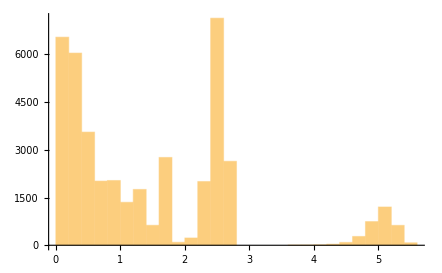
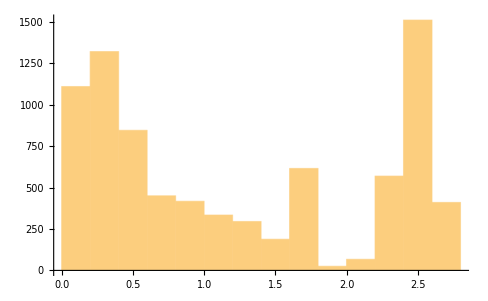

```mathematica
Map[{#[[1]],Last[#[[3]]],#[[4]],#[[5]]}&,list];
{Map[Log[#[[4]]]/#[[2]]&,Select[%,First[#]==0&]],Map[Log[#[[4]]]/#[[2]]&,Select[%,First[#]==1&]]};
{Histogram[%[[1]]],Histogram[%[[2]]]}
"Map[Mean,%];
Map[N,%]";
```

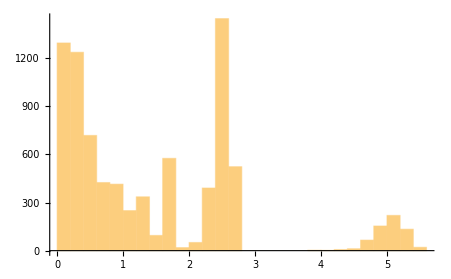
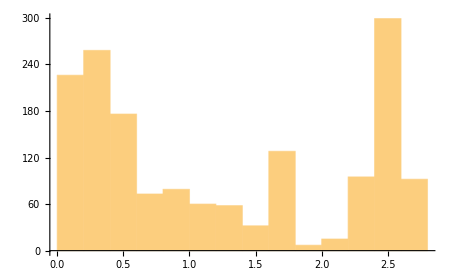

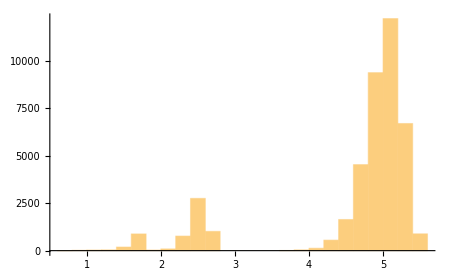
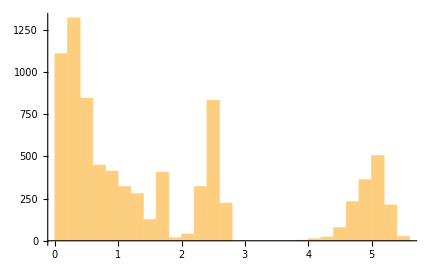

```mathematica
Map[{#[[1]],Piecewise[{{#[[3]][[1]], #[[1]]==0}, {#[[3]][[2]], #[[1]]==1}}],#[[4]],#[[5]]}&,list];
{Map[Log[#[[4]]]/#[[2]]&,Select[%,First[#]==0&]],Map[Log[#[[4]]]/#[[2]]&,Select[%,First[#]==1&]]};
{Histogram[%[[1]]],Histogram[%[[2]]]}
```

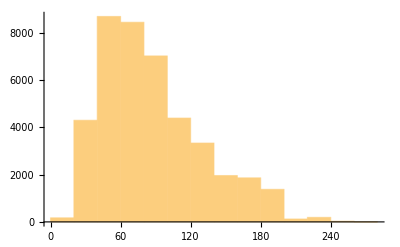
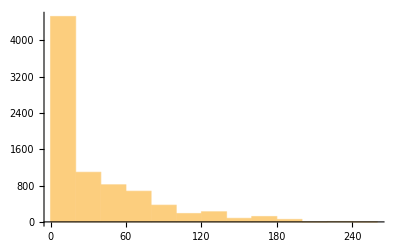

```mathematica
Map[{#[[1]],Piecewise[{{#[[3]][[1]], #[[1]]==0}, {#[[3]][[2]], #[[1]]==1}}],#[[4]],#[[5]]}&,list];
{Map[EulerPhi[#[[4]]]/#[[2]]&,Select[%,First[#]==0&]],Map[EulerPhi[#[[4]]]/#[[2]]&,Select[%,First[#]==1&]]};
{Histogram[%[[1]]],Histogram[%[[2]]]}
```

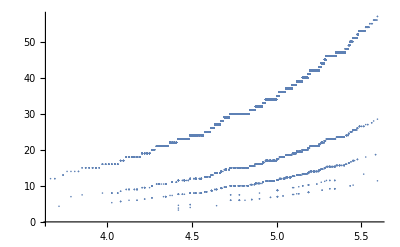
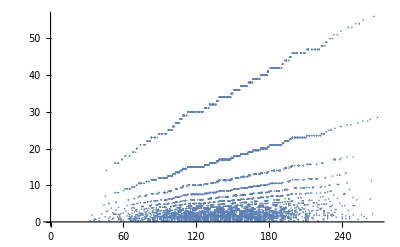

```mathematica
Map[{#[[1]],Piecewise[{{#[[3]][[1]], #[[1]]==0}, {#[[3]][[2]], #[[1]]==1}}],#[[4]],#[[5]]}&,list];
{Map[{Log[#[[4]]],(PrimePi[#[[4]]]/(#[[2]]))}&,Select[%,First[#]==0&]],Map[{#[[4]],(PrimePi[#[[4]]]/(#[[2]]))}&,Select[%,First[#]==1&]]};
Map[ListPlot,%]
```

```mathematica
Map[{Last[#[[3]]],#[[5]]}&,list];
Histogram[%]
```

$Aborted

{{11,90},{36,200},{5,139},{4,152},{2,143},{22,178},{2,137},{5,237},{36,128},{8,99},{3,151},{1,122},{2,135},{4,121},{2,207},{2,182},{50,153},{3,88},{13,100},{3,169},{8,144},{2,89},{8,106},{3,84},{6,135},{2,141},{16,186},{73,136},{16,90},{2,141},{1,168},{9,151},{2,133},{1,197},{52,102},{26,176},{189,190},{2,125},{2,146},{9,129},{2,163},{1,154},{2,134},49914,{3,118},{24,215},{2,105},{38,153},{20,141},{31,126},{2,133},{12,229},{6,175},{12,130},{53,161},{64,162},{2,189},{14,172},{6,201},{5,145},{10,134},{3,144},{58,148},{7,141},{2,157},{16,185},{3,169},{7,161},{28,175},{20,169},{47,144},{1,149},{2,150},{14,180},{4,186},{8,133},{2,177},{1,201},{2,182},{9,120},{36,191},{3,129},{3,154},{7,124},{66,127},{12,180},{15,166}}
 |  |  |  |

{{33,32},{34,6},{36,35},{37,17},{39,8},{40,39},{41,3},{42,16},{43,3},{44,3},{45,10},{46,12},{47,5},{48,47},{49,15},{50,20},{51,20},{52,14},{53,34},{54,12},{55,26},{56,27},{57,38},{58,57},{59,10},{60,40},{61,24},{62,8},{63,30},{64,44},{65,46},{66,65},{67,66},{68,46},{69,52},{70,50},{71,46},{72,71},{73,50},{74,73},{75,52},{76,75},{77,32},{78,54},{79,56},{80,79},{81,80},{82,81},{83,62},{84,83},{85,84},{86,85},{87,66},{88,87},{89,29},{90,64},{91,62},{92,91},{93,92},{94,70},{95,94},{96,95},{97,72},{98,97},{99,98},{100,99},{101,72},{102,101},{103,54},{104,76},{105,104},{106,105},{107,74},{108,107},{109,78},{110,109},{111,110},{112,111},{113,82},{114,113},{115,114},{116,88},{117,116},{118,117},{119,82},{120,119},{121,120},{122,86},{123,122},{124,123},{125,92},{126,125},{127,126},{128,127},{129,128},{130,129},{131,71},{132,131},{133,94},{134,96},{135,134},{136,135},{137,94},{138,137},{139,138},{140,139},{141,140},{142,79},{143,142},{144,143},{145,144},{146,96},{147,146},{148,147},{149,77},{150,84},{151,150},{152,80},{153,152},{154,153},{155,154},{156,155},{157,156},{158,81},{159,86},{160,159},{161,160},{162,161},{163,162},{164,81},{165,164},{166,165},{167,72},{168,167},{169,168},{170,169},{171,170},{172,171},{173,172},{174,173},{175,174},{176,175},{177,176},{178,74},{179,72},{180,179},{181,78},{182,181},{183,182},{184,183},{185,92},{186,185},{187,84},{188,80},{189,188},{190,189},{191,190},{192,191},{193,95},{194,76},{195,86},{196,195},{197,78},{198,197},{199,68},{200,199},{201,200},{202,86},{203,70},{204,203},{205,84},{206,71},{207,70},{208,207},{209,69},{210,209},{211,72},{212,211},{213,74},{214,73},{215,75},{216,73},{217,74},{218,72},{219,73},{220,219},{221,73},{222,77},{223,76},{224,77},{225,224},{226,66},{227,55},{228,80},{229,75},{230,37},{231,72},{232,77},{233,60},{234,72},{235,68},{236,70},{237,66},{238,70},{239,38},{240,70},{241,72},{242,68},{243,70},{244,36},{245,36},{246,62},{247,72},{248,72},{249,66},{250,16},{251,70},{252,9},{253,83},{254,15},{255,72},{256,74},{257,66},{258,38},{259,11},{260,65},{261,2},{263,66},{264,5},{265,26},{266,3},{268,28},{269,5}}

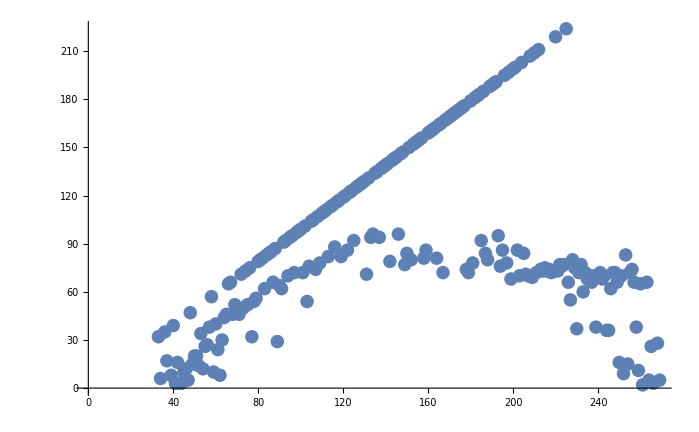

```mathematica
Map[{Last[#[[3]]],#[[5]]}&,list]
Table[{i,Max[Map[First,Select[%,#[[2]]==i&]]]},{i,Sort[DeleteDuplicates[Map[#[[5]]&,list]]]}]
ListPlot[%]
```

x

-37.6019+1.04918 x+0.0054773 x^2-0.0000329859 x^3

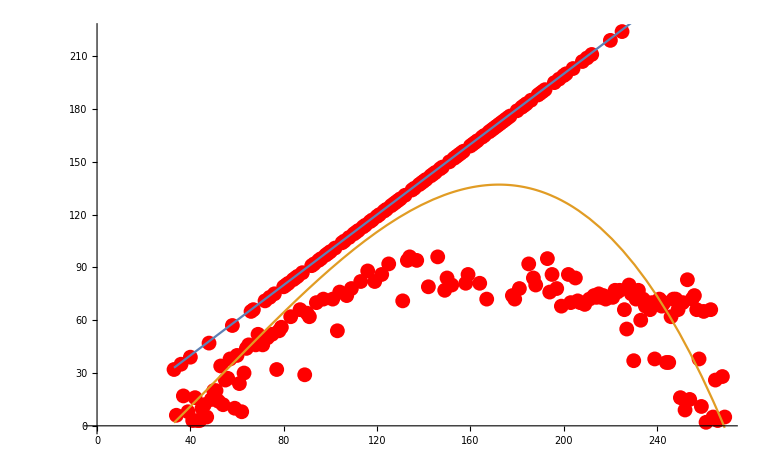

```mathematica
line=x(*Fit[Out[243],{1,x},x]*)
parabola=Fit[Out[243],{1,x,x^2,x^3},x]
Show[ListPlot[Out[243], PlotStyle->Red], Plot[{line, parabola}, {x, Min[Map[First,Out[243]]], Max[Map[First,Out[243]]]}]]
```

```mathematica
Map[First,Select[Out[243],1.035<#[[1]]/#[[2]]&]]
```

{34,37,39,41,42,43,44,45,46,47,49,50,51,52,53,54,55,56,57,59,60,61,62,63,64,65,68,69,70,71,73,75,77,78,79,83,87,89,90,91,94,97,101,103,104,107,109,113,116,119,122,125,131,133,134,137,142,146,149,150,152,158,159,164,167,178,179,181,185,187,188,193,194,195,197,199,202,203,205,206,207,209,211,213,214,215,216,217,218,219,221,222,223,224,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,263,264,265,266,268,269}

```mathematica
Table[%[[i+1]]-%[[i]],{i,1,Length[%]-1}]
```

{3,2,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,3,1,1,1,2,2,2,1,1,4,4,2,1,1,3,3,4,2,1,3,2,4,3,3,3,3,6,2,1,3,5,4,3,1,2,6,1,5,3,11,1,2,4,2,1,5,1,1,2,2,3,1,2,1,1,2,2,2,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1}

```mathematica
Tally[%]
```

{{3,13},{2,24},{1,86},{4,6},{6,2},{5,3},{11,1}}

```mathematica
EulerPhi[12]
```

4

```mathematica
DivisorSigma[0,12]
```

6

```mathematica
Divisors[12]
```

{1,2,3,4,6,12}

```mathematica
x==Log[y^5]
```

```mathematica
227/Log[228]//N
```

41.8098

```mathematica
leastmod[tlt_]:=Table[tf[MemberQ[Map[Mod[Total[#],mod]&,Subsets[DeleteCases[Map[Mod[#,mod]&,tlt],0]]],Total[Map[Mod[#,mod]&,tlt]]/2]],{mod,3,Total[tlt]}]
```

```mathematica
leastmod[{57,28,73,66,86}]
```

{1,1,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
First[Flatten[Position[Out[251],0]]]
```

3

```mathematica
Total[tl]
```

```mathematica
Mod[661299408,310/2]
```

123

```mathematica
Product[i,{i,tl}]
```

```mathematica
Table[Mod[310,i],{i,2,7}]
```

{0,1,2,0,4,2}

```mathematica
Mod[661299408,7]
```

0

```mathematica
GCD@@tl
```

1

```mathematica
Total[tl]
```

370

```mathematica
Product[i,{i,tl}]
```

```mathematica
Mod[4691887200,Total[tl]/2]
```

84

```mathematica
Mod[410158320,Total[tl]/2]
```

0

```mathematica
Mod[23550384000,3]
```

0

```mathematica
Mod[23550384000,370/2]
```

180

```mathematica
Map[Mod[180,#]&,tl]
```

```mathematica
228/2
```

114

```mathematica
Map[Total,Subsets[{4,86,24,34,80}]]
```

{0,4,86,24,34,80,90,28,38,84,110,120,166,58,104,114,114,124,170,62,108,118,144,190,200,138,148,194,204,142,224,228}

```mathematica
Sort[Map[Total,Subsets[tl]]]
```

{0,13,22,27,35,40,49,62,62,75,84,89,97,98,100,102,111,111,113,120,122,124,125,127,133,135,138,140,147,149,160,160,162,162,173,175,182,184,187,189,195,197,198,200,202,209,211,211,220,222,224,225,233,238,247,260,260,273,282,287,295,300,309,322}

```mathematica
370/2
```

185

```mathematica
tl=RandomInteger[{1,100},6]
```

{27,62,22,98,13,100}

```mathematica
Total[tl]
```

322

```mathematica
%/2
```

161

```mathematica
mod=3;
Total[Map[Mod[#,mod]&,tl]]/2
Sort[Map[Total,Subsets[DeleteCases[Map[Mod[#,mod]&,tl],0]]]]
```

7/2

{0,1,1,1,2,2,2,2,2,3,3,3,3,3,3,3,4,4,4,4,4,4,4,5,5,5,5,5,6,6,6,7}

```mathematica
pair[x_,y_]:=1/2(x+y)(x+y+1)+y
unpair[z_]:=Block[{w=Floor[(√(8z+1)-1)/2]},Block[{t=(w^2+w)/2},{w-(z-t),z-t}]]
unpair[pair[234,432]]
oct[{a_,b_,c_,d_,e_,f_,g_,h_}]:=pair[pair[pair[a,b],pair[c,d]],pair[pair[e,f],pair[g,h]]]
unoct[z_]:={unpair[unpair[unpair[z][[1]]][[1]]][[1]],unpair[unpair[unpair[z][[1]]][[1]]][[2]],unpair[unpair[unpair[z][[1]]][[2]]][[1]],unpair[unpair[unpair[z][[1]]][[2]]][[2]],unpair[unpair[unpair[z][[2]]][[1]]][[1]],unpair[unpair[unpair[z][[2]]][[1]]][[2]],unpair[unpair[unpair[z][[2]]][[2]]][[1]],unpair[unpair[unpair[z][[2]]][[2]]][[2]]}
unoct[oct[{1,2,3,4,5,6,7,8}]]
```

{234,432}

{1,2,3,4,5,6,7,8}

```mathematica
Timing[blist=Monitor[Table[tf[MemberQ[Map[Total,Subsets[DeleteCases[unoct[k],0]]],Total[unoct[k]]/2]],{k,1,10000}],k];]
```

{13.31063,Null}

```mathematica
Monitor[Table[{int[First[Flatten[Position[leastmod2[unoct[k]],tf[MemberQ[Map[Total,Subsets[DeleteCases[unoct[k],0]]],Total[unoct[k]]/2]]]]]]/Total[unoct[k]]},{k,16,100000}],k];
Histogram[%]
```

First::nofirst: {} has a length of zero and no first element.

General::stop: Further output of First :: nofirst will be suppressed during this calculation.

$Aborted

```mathematica
Select[Out[421],#[[1]]==0&]
```

{{0,2},{0,2},{0,1},{0,2},{0,2},{0,2},{0,2},{0,2},{0,2},{0,3},{0,2},{0,2},{0,3},{0,2},{0,2},{0,3},{0,2},{0,2},{0,3},{0,2},{0,2},{0,3},{0,3},{0,2},{0,2},{0,3},{0,2},{0,3},{0,2},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,2},{0,3},{0,3},{0,2},{0,3},{0,3},{0,2},{0,3},{0,3},{0,2},{0,2},{0,2},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,2},{0,3},{0,3},{0,2},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3},{0,3}}

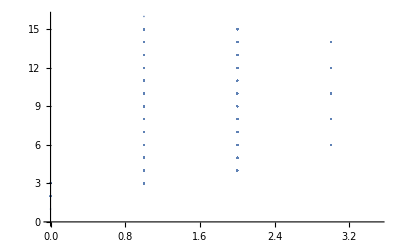

```mathematica
ListPlot[Out[421]]
```

```mathematica
DeleteDuplicates[Map[tf[IntegerQ[#[[1]]]]+tf[IntegerQ[#[[2]]]]&,Out[421]]]
```

{2}

```mathematica
leastmod2[tlt_]:=Table[tf[MemberQ[Map[Mod[Total[#],mod]&,Subsets[DeleteCases[Map[Mod[#^2,mod]&,tlt],0]]],Total[Map[Mod[#^2,mod]&,tlt]]/2]],{mod,3,Total[tlt]}]
```

```mathematica
unoct[100]
```

{1,0,1,0,0,0,2,0}

```mathematica
leastmod2[unoct[100]]
```

{0,1}

```mathematica
37 Subscript[x, 1]+17 Subscript[x, 2]+5 Subscript[x, 3]+33 Subscript[x, 4]+76 Subscript[x, 5]+52 Subscript[x, 6]-Total[{37,17,5,33,76,52}]/2==min
0≤Subscript[x, 1]≤1
0≤Subscript[x, 2]≤1
0≤Subscript[x, 3]≤1
0≤Subscript[x, 4]≤1
0≤Subscript[x, 5]≤1
0≤Subscript[x, 6]≤1
```

```mathematica
tl0=RandomInteger[{1,1000},12]
Total[%]
%/2
Position[Sort[Map[Total,Subsets[tl0]]],%]
```

{122,100,618,590,5,650,710,614,913,429,770,391}

5912

2956

{{2048},{2049}}

```mathematica
Select[Subsets[tl0],Total[#]==2956&]
```

{{618,5,650,913,770},{122,100,590,710,614,429,391}}

```mathematica
Sort[{122,100,618,590,5,650,710,614,913,429,770,391}]
```

```mathematica
{5,100,122,391,429,590,614,618,650,710,770,913}
```

1

```mathematica
FactorInteger[2956]
```

{{2,2},{739,1}}

```mathematica
DivisorSigma[0,2956]
```

6

```mathematica
Mod[2956,6]
```

4

```mathematica
Mod[Total[{23,1,24,29,5,23,17,20,22,0,11,28}],33]
```

5

```mathematica
Map[Mod[#,33]&,{122,100,618,590,5,650,710,614,913,429,770,391}]
```

{23,1,24,29,5,23,17,20,22,0,11,28}

```mathematica
Select[Map[Mod[Total[#],33]&,Subsets[{23,1,24,29,5,23,17,20,22,0,11,28}]],#==5&]
```

{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

```mathematica
Length[Out[226]]
```

116

```mathematica
Map[Mod[#^2,6]&,{122,100,618,590,5,650,710,614,913,429,770,391}]
```

{4,4,0,4,1,4,4,4,1,3,4,1}

```mathematica
DiscretePlot3D[Total[Map[tf[Mod[Total[#],i]==j]&,Subsets[{122,100,618,590,5,650,710,614,913,429,770,391}]]],{i,3,19},{j,0,19}]
```

-Graphics3D-

```mathematica
diff[list_]:=Table[list[[i+1]]-list[[i]],{i,1,Length[list]-1}]
```

```mathematica
Sort[{122,100,618,590,5,650,710,614,913,429,770,391}]
```

```mathematica
Sort[diff[{5,100,122,391,429,590,614,618,650,710,770,913}]]
```

```mathematica
Sort[diff[{4,22,24,32,38,60,60,95,143,161,269}]]
```

```mathematica
Sort[diff[{0,2,6,8,18,18,22,35,48,108}]]
```

```mathematica
Sort[diff[{0,2,2,4,4,10,13,13,60}]]
```

```mathematica
Sort[diff[{0,0,0,2,2,3,6,47}]]
```

```mathematica
Sort[diff[{0,0,0,1,2,3,41}]]
```

```mathematica
Sort[diff[{0,0,1,1,1,38}]]
```

```mathematica
Sort[diff[{0,0,0,1,37}]]
```

```mathematica
Sort[diff[{0,0,1,36}]]
```

```mathematica
Sort[diff[{0,1,35}]]
```

```mathematica
Sort[diff[{1,34}]]
```

{33}

```mathematica
{5,100,122,391,429,590,614,618,650,710,770,913}
diff[{5,100,122,391,429,590,614,618,650,710,770,913}]
diff[diff[{5,100,122,391,429,590,614,618,650,710,770,913}]]
diff[diff[diff[{5,100,122,391,429,590,614,618,650,710,770,913}]]]
diff[diff[diff[diff[{5,100,122,391,429,590,614,618,650,710,770,913}]]]]
diff[diff[diff[diff[diff[{5,100,122,391,429,590,614,618,650,710,770,913}]]]]]
diff[diff[diff[diff[diff[diff[{5,100,122,391,429,590,614,618,650,710,770,913}]]]]]]
diff[diff[diff[diff[diff[diff[diff[{5,100,122,391,429,590,614,618,650,710,770,913}]]]]]]]
diff[diff[diff[diff[diff[diff[diff[diff[{5,100,122,391,429,590,614,618,650,710,770,913}]]]]]]]]
diff[diff[diff[diff[diff[diff[diff[diff[diff[{5,100,122,391,429,590,614,618,650,710,770,913}]]]]]]]]]
diff[diff[diff[diff[diff[diff[diff[diff[diff[diff[{5,100,122,391,429,590,614,618,650,710,770,913}]]]]]]]]]]
diff[diff[diff[diff[diff[diff[diff[diff[diff[diff[diff[{5,100,122,391,429,590,614,618,650,710,770,913}]]]]]]]]]]]
```

{5,100,122,391,429,590,614,618,650,710,770,913}

{95,22,269,38,161,24,4,32,60,60,143}

{-73,247,-231,123,-137,-20,28,28,0,83}

{320,-478,354,-260,117,48,0,-28,83}

{-798,832,-614,377,-69,-48,-28,111}

{1630,-1446,991,-446,21,20,139}

{-3076,2437,-1437,467,-1,119}

{5513,-3874,1904,-468,120}

{-9387,5778,-2372,588}

{15165,-8150,2960}

{-23315,11110}

{34425}

```mathematica
fe={{5,100,122,391,429,590,614,618,650,710,770,913},
{0,95,22,269,38,161,24,4,32,60,60,143},
{0,0,-73,247,-231,123,-137,-20,28,28,0,83},
{0,0,0,320,-478,354,-260,117,48,0,-28,83},
{0,0,0,0,-798,832,-614,377,-69,-48,-28,111},
{0,0,0,0,0,1630,-1446,991,-446,21,20,139},
{0,0,0,0,0,0,-3076,2437,-1437,467,-1,119},
{0,0,0,0,0,0,0,5513,-3874,1904,-468,120},
{0,0,0,0,0,0,0,0,-9387,5778,-2372,588},
{0,0,0,0,0,0,0,0,0,15165,-8150,2960},
{0,0,0,0,0,0,0,0,0,0,-23315,11110},
{0,0,0,0,0,0,0,0,0,0,0,34425}};
```

```mathematica
fee=Transpose[UpperTriangularize[fe,1]]+fe;
%//MatrixForm
```

(5 | 100 | 122 | 391 | 429 | 590 | 614 | 618 | 650 | 710 | 770 | 913
100 | 95 | 22 | 269 | 38 | 161 | 24 | 4 | 32 | 60 | 60 | 143
122 | 22 | -73 | 247 | -231 | 123 | -137 | -20 | 28 | 28 | 0 | 83
391 | 269 | 247 | 320 | -478 | 354 | -260 | 117 | 48 | 0 | -28 | 83
429 | 38 | -231 | -478 | -798 | 832 | -614 | 377 | -69 | -48 | -28 | 111
590 | 161 | 123 | 354 | 832 | 1630 | -1446 | 991 | -446 | 21 | 20 | 139
614 | 24 | -137 | -260 | -614 | -1446 | -3076 | 2437 | -1437 | 467 | -1 | 119
618 | 4 | -20 | 117 | 377 | 991 | 2437 | 5513 | -3874 | 1904 | -468 | 120
650 | 32 | 28 | 48 | -69 | -446 | -1437 | -3874 | -9387 | 5778 | -2372 | 588
710 | 60 | 28 | 0 | -48 | 21 | 467 | 1904 | 5778 | 15165 | -8150 | 2960
770 | 60 | 0 | -28 | -28 | 20 | -1 | -468 | -2372 | -8150 | -23315 | 11110
913 | 143 | 83 | 83 | 111 | 139 | 119 | 120 | 588 | 2960 | 11110 | 34425)

```mathematica
fe3=fee*1/(2^(1/3) 674409910783120501886846896504233908633^(1/12));
```